# HRV Code

https://twitter.com/nntaleb/status/1737118358401945954

```mathematica
?Accumulate
```

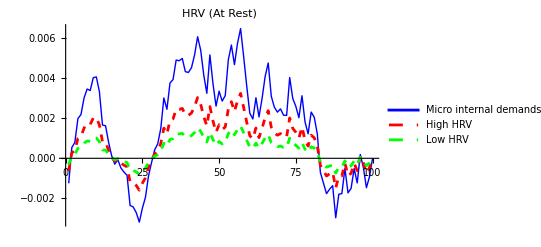

```mathematica
X=RandomVariate[NormalDistribution[0,0.001],100];
Y1=X-Mean[X] // Accumulate;
Y2=(X - Mean[X]) * .5 // Accumulate;
Y3 =(X - Mean[X]) * .25 // Accumulate;
ListLinePlot[{Y1,Y2, Y3}, PlotStyle->{{Blue, Thin}, {Red,Dashed}, {Green,Dashed}},Ticks->{Automatic, None},PlotLegends->{"Micro internal demands from the environment","High HRV","Low HRV"},PlotLabel->"HRV (At Rest)"]
```